# From 2 to 3 measurements

```mathematica
Clear["Global`*"]
```

## Defining and visualizing the measurements

```mathematica
(* Medições parametrizadas pelos vetores de Bloch *)
q1:={0,0,1}
q2[θ_]:={Sin[θ],0,Cos[θ]}
q3[θ_]:={Sin[-θ],0,Cos[-θ]}

(* Utilitário pra desenhar arcos de circunferência em 3D *)
arc[center_?VectorQ,{start_?VectorQ,end_?VectorQ}]:=Module[{ang,co,r},ang=VectorAngle[start-center,end-center];
co=Cos[ang/2];r=EuclideanDistance[center,start];
{Thickness->Medium,BSplineCurve[{start,center+r/co Normalize[(start+end)/2-center],end},SplineDegree->2,SplineKnots->{0,0,0,1,1,1},SplineWeights->{1,co,1}]}]

(* Draw Bloch ball and measurement vectors *)
arcLength:=.2
Manipulate[Graphics3D[{{Dashed,Line[{{0,0,0},{1.3,0,0}}]},
{Dashed,Line[{{0,0,0},{0,1.3,0}}]},
{Dashed,Line[{{0,0,0},{0,0,1.3}}]},
{Arrowheads[Medium],Arrow[{{1.3,0,0},{1.4,0,0}}]},
{Arrowheads[Medium],Arrow[{{0,1.3,0},{0,1.4,0}}]},
{Arrowheads[Medium],Arrow[{{0,0,1.3},{0,0,1.4}}]},
Text[Style["x",18],{1.6,0,0}],
Text[Style["y",18],{0,1.6,0}],
Text[Style["z",18],{0,0,1.6}],
{Thick,Arrow[{{0,0,0},q1}]},
{Thick,Arrow[{{0,0,0},q2[θ]}]},
{Thick,Arrow[{{0,0,0},q3[θ]}]},
{arc[{0,0,0},{{0,0,arcLength},arcLength{Sin[θ],0,Cos[θ]}}]},
{arc[{0,0,0},{{0,0,arcLength},arcLength{Sin[-θ],0,Cos[-θ]}}]},
{Text[Style["θ",FontSize->13],1.5arcLength q2[θ/2]]},
{Text[Style["θ",FontSize->13],1.5arcLength q3[θ/2]]},
{Glow[Blue],Opacity[.28],Cylinder[{{0,0,-.0001},{0,0,.0001}}]},
{Glow[Blue],Opacity[.28],Cylinder[{{0,0,-.0001},{0,0,.0001}}]},
{Blue,Opacity[.18],Sphere[]}},
(*{Text[Style["θ = " θ,FontSize->13,FontWeight->Bold],{0,0,2}]}},*)
Boxed->False,ImageSize->Large,ViewPoint->{2.1Pi/3,1.3Pi/2,1.3Pi/4}],
{θ,0,Pi},ContentSize->Large]
```

## Activation form 2-3 measurements with max. violation of S_2233

```mathematica
(*Vetores de estado da preparação*)
r1[κ_,α_,β_]:=κ {Sin[α] Cos[β],Sin[α] Sin[β],Cos[α]}
r2[κ_,γ_,δ_]:=κ {Sin[γ] Cos[δ],Sin[γ] Sin[δ],Cos[γ]}
r3[κ_,μ_,ν_]:=κ {Sin[μ] Cos[ν],Sin[μ] Sin[ν],Cos[μ]}

(* Conds da eq.13 do PAM_Bell: equivale a Subscript[S, 2232] não ser violada pra nenhum par de medições *)
NaoViolaS2232[r1_,r2_,r3_]:=Norm[r1+r2-r3]+Norm[r1-r2]≤3&&Norm[r1+r3-r2]+Norm[r1-r3]≤3&&Norm[r3+r2-r1]+Norm[r3-r2]≤3

(* Desigualdade que queremos violar: eq. 32 do PAM_Bell *)
S2233[r1_,r2_,r3_,q1_,q2_,q3_]:=r1.q1+r1.q2-r2.q2+r2.q3-r3.q1-r3.q3

(* Encontra estados que maximizam a violação *)
maxViolation=NMaximize[{S2233[r1[κ,α,β],r2[κ,γ,δ],r3[κ,μ,ν],q1,q2[θ],q3[θ]],NaoViolaS2232[r1[κ,α,β],r2[κ,γ,δ],r3[κ,μ,ν]]},{{κ,0,1},{α,0,2 Pi},{β,0,2 Pi},{γ,0,2 Pi},{δ,0,2 Pi},{μ,0,2 Pi},{ν,0,2 Pi},{θ,0,Pi}},Method->{"RandomSearch","SearchPoints"->250}]
```

{4.17691,{κ→0.803848,α→-0.523599,β→3.14159,γ→1.5708,δ→3.14159,μ→3.66519,ν→3.14159,θ→1.0472}}

```mathematica
(* Visualize optimized measurements (red) and preparations (blue) *)
Graphics3D[{{Dashed,Line[{{0,0,0},{1.3,0,0}}]},
{Dashed,Line[{{0,0,0},{0,1.3,0}}]},
{Dashed,Line[{{0,0,0},{0,0,1.3}}]},
{Arrowheads[Medium],Arrow[{{1.3,0,0},{1.4,0,0}}]},
{Arrowheads[Medium],Arrow[{{0,1.3,0},{0,1.4,0}}]},
{Arrowheads[Medium],Arrow[{{0,0,1.3},{0,0,1.4}}]},
Text[Style["x",18],{1.6,0,0}],
Text[Style["y",18],{0,1.6,0}],
Text[Style["z",18],{0,0,1.6}],
{Thick,Red,Arrow[{{0,0,0},q1}]},
{Thick,Red,Arrow[{{0,0,0},q2[θ]/.maxViolation[[2]]}]},
{Thick,Red,Arrow[{{0,0,0},q3[θ]/.maxViolation[[2]]}]},
{Thick,Opacity[.3],Red,Dashed,Arrow[{{0,0,0},-q1}]},
{Thick,Opacity[.3],Red,Dashed,Arrow[{{0,0,0},-q2[θ]/.maxViolation[[2]]}]},
{Thick,Opacity[.3],Red,Dashed,Arrow[{{0,0,0},-q3[θ]/.maxViolation[[2]]}]},
{Thick,Blue,Arrow[{{0,0,0},r1[κ,α,β]/.maxViolation[[2]]}]},
{Thick,Blue,Arrow[{{0,0,0},r2[κ,γ,δ]/.maxViolation[[2]]}]},
{Thick,Blue,Arrow[{{0,0,0},r3[κ,μ,ν]/.maxViolation[[2]]}]},
{Glow[Blue],Opacity[.28],Cylinder[{{0,0,-.0001},{0,0,.0001}}]},
{Glow[Blue],Opacity[.28],Cylinder[{{0,0,-.0001},{0,0,.0001}}]},
{Blue,Opacity[.18],Sphere[]}},Boxed->False,ImageSize->Medium]
```

-Graphics3D-

## S_2233 for optimal preparations and arbitrary measurements

```mathematica
(* Substituting optimization angles only on preparations *)
optS2233=FullSimplify[S2233[r1[κ,α,β],r2[κ,γ,δ],r3[κ,μ,ν],q1,q2[ϕ],q3[ϕ]]]/.Drop[maxViolation[[2]],1]

(* Same thing but with analytical approximation and arbitrary κ
I put κ on the measurements to make preparations pure: it's the same in the end *)
FullSimplify[S2233[r1[1,-Pi/6,Pi],r2[1,Pi/2,Pi],r3[1,7 Pi/6,Pi],κ q1,κ q2[ϕ],κ q3[ϕ]]]
```

1.73205 κ (1+Cos[ϕ])+3. κ Sin[ϕ]

κ (√3+√3 Cos[ϕ]+3 Sin[ϕ])

```mathematica
(* Solve bound of preparation optimized Subscript[S, 2233] and plot violation region *)
```

{{κ→4./(1.73205 (1.+Cos[ϕ])+3. Sin[ϕ])}}

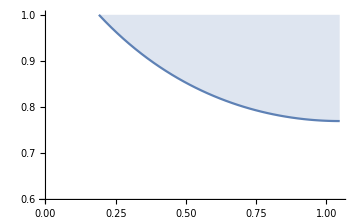

```mathematica
Solve[optS2233==4,κ]
Plot[%[[1,1,2]],{ϕ,0,Pi/3},PlotRange->{0.6,1},ImageSize->Medium,Filling->Top]
```

```mathematica
(* And these are the optimal preparations and measurements directions (I dropped the visibility) *)
optPreps={r1[1,-Pi/6,Pi],r2[1,Pi/2,Pi],r3[1,7 Pi/6,Pi]}
optMeas={q1,q2[Pi/3],q3[Pi/3]}
```

{{1/2,0,(√3)/2},{-1,0,0},{1/2,0,-(√3)/2}}

{{0,0,1},{(√3)/2,0,1/2},{-(√3)/2,0,1/2}}

Comments: I ran our program to search for a classical measurements model in a range that would show activation, but couldn’t find. As a matter of fact, the local curve was still pretty lower than the one traced above. This is mainly because our method will always depolarize the structure we’re testing (in this case, the measurements), and as the maximum violation for this type of activation was only ~4.17, there is not much margin for mixing. The next step is to investigate higher scenarios, such as activation from 3 to 4 measurements, or even 2 to 4.

# From 2 to 4 measurements

```mathematica
Clear["Global`*"]
```

## Defining and visualizing the measurements

```mathematica
(* Medições parametrizadas pelos vetores de Bloch *)
q1:={0,0,1}
q2:=-{0,0,1}
q3[θ_]:={Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]}/.ϕ->0
q4[θ_]:={Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]}/.ϕ->Pi
(* q4[θ_]:={Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]}/.ϕ->4 Pi/3 *)

(* Utilitário pra desenhar arcos de circunferência em 3D *)
arc[center_?VectorQ,{start_?VectorQ,end_?VectorQ}]:=Module[{ang,co,r},ang=VectorAngle[start-center,end-center];
co=Cos[ang/2];r=EuclideanDistance[center,start];
{Thickness->Medium,BSplineCurve[{start,center+r/co Normalize[(start+end)/2-center],end},SplineDegree->2,SplineKnots->{0,0,0,1,1,1},SplineWeights->{1,co,1}]}]

(* Draw Bloch ball and measurement vectors *)
arcLength:=.2
Manipulate[Graphics3D[{{Dashed,Line[{{0,0,0},{1.3,0,0}}]},
{Dashed,Line[{{0,0,0},{0,1.3,0}}]},
{Dashed,Line[{{0,0,0},{0,0,1.3}}]},
{Arrowheads[Medium],Arrow[{{1.3,0,0},{1.4,0,0}}]},
{Arrowheads[Medium],Arrow[{{0,1.3,0},{0,1.4,0}}]},
{Arrowheads[Medium],Arrow[{{0,0,1.3},{0,0,1.4}}]},
Text[Style["x",18],{1.6,0,0}],
Text[Style["y",18],{0,1.6,0}],
Text[Style["z",18],{0,0,1.6}],
{Thick,Arrow[{{0,0,0},q1}]},
{Thick,Arrow[{{0,0,0},q2}]},
{Thick,Arrow[{{0,0,0},q3[θ]}]},
{Thick,Arrow[{{0,0,0},q4[θ]}]},
{arc[{0,0,0},{{0,0,arcLength},arcLength q2}]},
{arc[{0,0,0},{{0,0,arcLength},arcLength q3[θ]}]},
{arc[{0,0,0},{{0,0,arcLength},arcLength q4[θ]}]},
(*{Text[Style["θ",FontSize->13],1.5arcLength q2[θ/2]]},*)
{Text[Style["θ",FontSize->13],1.5arcLength q3[θ/2]]},
{Text[Style["θ",FontSize->13],1.5arcLength q4[θ/2]]},
{Glow[Blue],Opacity[.28],Cylinder[{{0,0,-.0001},{0,0,.0001}}]},
{Glow[Blue],Opacity[.28],Cylinder[{{0,0,-.0001},{0,0,.0001}}]},
{Blue,Opacity[.18],Sphere[]}},
(*{Text[Style["θ = " θ,FontSize->13,FontWeight->Bold],{0,0,2}]}},*)
Boxed->False,ImageSize->Large,ViewPoint->{2.1Pi/3,1.3Pi/2,1.3Pi/4}],
{θ,0,Pi},ContentSize->Large]
```

## Activation form 2-4 measurements with max. violation of an S_2234 ineq.

```mathematica
(*Vetores de estado da preparação*)
r1[κ_,α_,β_]:=κ {Sin[α] Cos[β],Sin[α] Sin[β],Cos[α]}
r2[κ_,γ_,δ_]:=κ {Sin[γ] Cos[δ],Sin[γ] Sin[δ],Cos[γ]}
r3[κ_,μ_,ν_]:=κ {Sin[μ] Cos[ν],Sin[μ] Sin[ν],Cos[μ]}

(* Conds da eq.13 do PAM_Bell: equivale a Subscript[S, 2232] não ser violada pra nenhum par de medições *)
NaoViolaS2232[r1_,r2_,r3_]:=Norm[r1+r2-r3]+Norm[r1-r2]≤3&&Norm[r1+r3-r2]+Norm[r1-r3]≤3&&Norm[r3+r2-r1]+Norm[r3-r2]≤3

(* Desigualdade que queremos violar: *)
(* 1 1 1 0 1 -1 -1 0 -1 -1 1 0 -3 *)
S1[r1_,r2_,r3_,q1_,q2_,q3_]:=r1.q1+r1.q2+r1.q3+r2.q1-r2.q2-r2.q3-r3.q1-r3.q2+r3.q3
(* 1 1 -1 0 -1 1 1 0 1 -1 1 0 -4 *)
S2[r1_,r2_,r3_,q1_,q2_,q3_]:=r1.q1+r1.q2-r1.q3-r2.q1+r2.q2+r2.q3+r3.q1-r3.q2+r3.q3
(* 1 0 1 0   -1 1 0 0    0 -1 -1 0   -2 *)
S3[r1_,r2_,r3_,q1_,q2_,q3_]:=r1.q1+r1.q3-r2.q1+r2.q2-r3.q2-r3.q3
(* -1 -1 0 0    1 0 0 -1    0 1 0 1 -2 *)

(* Encontra estados que maximizam a violação *)
maxViolation=NMaximize[{S1[r1[κ,α,β],r2[κ,γ,δ],r3[κ,μ,ν],q1,q2,q3[θ]],NaoViolaS2232[r1[κ,α,β],r2[κ,γ,δ],r3[κ,μ,ν]]},{{κ,0,1},{α,0,2 Pi},{β,0,2 Pi},{γ,0,2 Pi},{δ,0,2 Pi},{μ,0,2 Pi},{ν,0,2 Pi},{θ,0,Pi}}]
```

{9.,{κ→3.,α→6.28319,β→3.97,γ→6.28319,δ→9.84693,μ→6.28319,ν→6.74835,θ→-3.79392×10^-6}}

Comments: I tested (kinda manually) for the families of inequalities in this scenario and could find no violation whatsoever (while not violation S_2233).  I messed a little with the measurements to no luck. Is it strange that S_2234 inequalities only ever use 3 measurements at a time?